```mathematica
ep=0.08;β=0.8;γ=0.5;xmin=-50;xmax=50;maxtime=100;
(*Gap parameters*)
```

```mathematica
eqn=FindRoot[v-v^3/3-(v+β)/γ,{v,-1}];
{v0,w0}={v,(v+β)/γ}/.eqn;

(*d2=0.8;ρ[x_]=d2*Which[Abs[x] <=1, 1, True, 0];(*no block*)*)
(*d2=0.9;ρ[x_]=d2*Which[Abs[x] <=1, 1, True, 0];(*no block*)*)
(*d2=1;ρ[x_]=d2*Which[Abs[x] <=1, 1, True, 0];(*block*)*)
(*d2=1.2;ρ[x_]=d2*Which[Abs[x] <=1, 1, True, 0];(*block*)*)
(*d1=3;d2=1.2;ρ[x_]=d2*d1^(3/2)/(d1+x^2)^(3/2);(*block*)*)
(*d1=3;d2=1.1;ρ[x_]=d2*d1^(3/2)/(d1+x^2)^(3/2);(*block*)*)
d1=3;d2=1;ρ[x_]=d2*d1^(3/2)/(d1+x^2)^(3/2);(*no block*)
δ=0.1; (*slope parameter *)
(*Which[t<1/δ,δ t,True,1]*)
{V1,W1}=NDSolveValue[{D[u[t, x], t] == 0.5D[u[t, x], x, x] + u[t, x](1-ρ[x]^2/2) -u[t,x]^3/3 - w[t,x], D[w[t, x], t] == 0.001 D[w[t, x], x, x] + ep (u[t, x] - γ w[t, x]+β), 
u[0, x] == v0, 
u[t, xmin] == v0, 
u[t, xmax] == v0, w[0, x] ==w0, w[t, xmin] == w0,w[t, xmax] == w0}, {u, w}, {t, 0, 200}, {x, xmin, xmax}]
{V2,W2}=NDSolveValue[{D[u[t, x], t] == 0.5D[u[t, x], x, x] + u[t, x](1-ρ[x]^2/2) -u[t,x]^3/3 - w[t,x], D[w[t, x], t] == 0.001 D[w[t, x], x, x] + ep (u[t, x] - γ w[t, x]+β), 
u[0, x] == V1[200,x](*-Which[Abs[x+45] <=1, 3, True, 0]*), 
u[t, xmin] == v0, 
u[t, xmax] == v0, w[0, x] ==W1[200,x], w[t, xmin] == w0,w[t, xmax] == w0}, {u, w}, {t, 0, maxtime}, {x, xmin, xmax}]
{V,W}=NDSolveValue[{D[u[t, x], t] == 0.5D[u[t, x], x, x] + u[t, x](1-ρ[x]^2/2) -u[t,x]^3/3 - w[t,x], D[w[t, x], t] == 0.001 D[w[t, x], x, x] + ep (u[t, x] - γ w[t, x]+β), 
u[0, x] == V2[maxtime,x]+Which[Abs[x+45] <=1, 3, True, 0], 
u[t, xmin] == v0, 
u[t, xmax] == v0, w[0, x] ==W2[maxtime,x], w[t, xmin] == w0,w[t, xmax] == w0}, {u, w}, {t, 0, maxtime}, {x, xmin, xmax}]

(*Look for stationary solution*)
(*{V1,W1}=NDSolveValue[{D[u[t, x], t] == 0.5D[u[t, x], x, x] + u[t, x](1-Which[t<1/δ,δ t,True,1]ρ[x]^2/2) -u[t,x]^3/3 - w[t,x], D[w[t, x], t] == 0.001 D[w[t, x], x, x] + ep (u[t, x] - γ w[t, x]+β), 
u[0, x] == v0, 
u[t, xmin] == v0, 
u[t, xmax] == v0, w[0, x] ==w0, w[t, xmin] == w0,w[t, xmax] == w0}, {u, w}, {t, 0, 100}, {x, xmin, xmax}]*)
(*+Which[Abs[x+45] <=1, 3, True, 0]*)
(*Neumann , 
Derivative[0, 1][u][t, xmin] == 0, Derivative[0, 1][u][t, xmax] == 0, w[0, x] ==w0, Derivative[0, 1][w][t, xmin] == 0,Derivative[0, 1][w][t, xmax] == 0
*)
```

{InterpolatingFunction[…],InterpolatingFunction[…]}

NDSolveValue::mxsst: Using maximum number of grid points 10000 allowed by the MaxPoints or MinStepSize options for independent variable x.

{InterpolatingFunction[{{0., 100.}, {-50., 50.}}, <>],InterpolatingFunction[{{0., 100.}, {-50., 50.}}, <>]}

NDSolveValue::mxsst: Using maximum number of grid points 10000 allowed by the MaxPoints or MinStepSize options for independent variable x.

{InterpolatingFunction[{{0., 100.}, {-50., 50.}}, <>],InterpolatingFunction[{{0., 100.}, {-50., 50.}}, <>]}

```mathematica
Animate[Plot[{V[t,x],W[t,x],1-ρ[x]^2/2},{x,xmin,xmax},PlotRange->{{xmin,xmax},{-2,2}}],{t,0,maxtime}]
Plot3D[V[t,x], {t, 0, maxtime}, {x, xmin, xmax},PlotRange->{-2,2},AxesLabel->{"time","space"},Mesh->All]
```

-Graphics3D-

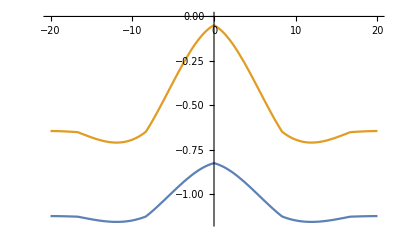

```mathematica
(*Standing Waves 2*)
xmin=-100;xmax=100;maxtime=500;
{V1,W1}=NDSolveValue[{D[u[t, x], t] == 0.5D[u[t, x], x, x] + u[t, x](1-ρ[x]^2/2) -u[t,x]^3/3 - w[t,x], D[w[t, x], t] == 0.001 D[w[t, x], x, x] + ep (u[t, x] - γ w[t, x]+β), 
u[0, x] == v0, 
u[t, xmin] == v0, 
u[t, xmax] == v0, w[0, x] ==w0, w[t, xmin] == w0,w[t, xmax] == w0}, {u, w}, {t, 0, maxtime}, {x, xmin, xmax}];
Plot[{V1[maxtime,x],W1[maxtime,x]},{x,-20,20}]
Animate[Plot[{V1[t,x],W1[t,x],0.5Derivative[0, 2][V1][t, x] + V1[t, x](1-ρ[x]^2/2) -V1[t,x]^3/3 - W1[t,x]},{x,-20,20},PlotRange->{{-20,20},{-2,2}}],{t,0,100}]
```